# Diplomado en programación básica

## 31 de enero de 2023

## Luis Gerardo Ramírez Archundia

## Series y tablas

```mathematica
Table[{i,i*0.1},{i,0,10}]
```

{{0,0.},{1,0.1},{2,0.2},{3,0.3},{4,0.4},{5,0.5},{6,0.6},{7,0.7},{8,0.8},{9,0.9},{10,1.}}

```mathematica
Table[Prime[i],{i,1,10}]
```

{2,3,5,7,11,13,17,19,23,29}

```mathematica
Table[{x,N[Cos[x]],N[Sin[x]],N[Tan[x]]},{x,0,10}]
```

(0 | 1. | 0. | 0.
1 | 0.540302 | 0.841471 | 1.55741
2 | -0.416147 | 0.909297 | -2.18504
3 | -0.989992 | 0.14112 | -0.142547
4 | -0.653644 | -0.756802 | 1.15782
5 | 0.283662 | -0.958924 | -3.38052
6 | 0.96017 | -0.279415 | -0.291006
7 | 0.753902 | 0.656987 | 0.871448
8 | -0.1455 | 0.989358 | -6.79971
9 | -0.91113 | 0.412118 | -0.452316
10 | -0.839072 | -0.544021 | 0.648361)

## Ejercicios

Calcular las siguientes operaciones

```mathematica
Sin[45 Degree]
```

1/(√2)

```mathematica
Cos[90 Degree]
```

0

```mathematica
Tan[Pi/2]
```

ComplexInfinity

```mathematica
Exp[0]
```

1

```mathematica
ArcCos[0]
```

π/2

```mathematica
Sin[Pi/2]
```

1

```mathematica
Tan[0]
```

0

```mathematica
ExpToTrig[Exp[I θ]]
```

Cos[θ]+ⅈ Sin[θ]

```mathematica
ExpToTrig[Exp[-x]]
```

Cosh[x]-Sinh[x]

```mathematica
N[Log[10]]
```

2.30259

```mathematica
N[Log[50]]
```

3.91202

```mathematica
N[Log[0]]
```

-∞

```mathematica
Sec[4 Degree]
```

Sec[4 °]

```mathematica
1/0
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
Sin[90 Degree]
```

1

```mathematica
Sqrt[8769]
```

√8769

Expandir las siguientes expresiones usando el comando TrigExpand

```mathematica
TrigExpand[Sin[2x]]
```

2 Cos[x] Sin[x]

```mathematica
TrigExpand[Sin[3 x]]
```

3 Cos[x]^2 Sin[x]-Sin[x]^3

```mathematica
TrigExpand[Cos[2x]]
```

Cos[x]^2-Sin[x]^2

```mathematica
TrigExpand[Tanh[2x]]
```

(2 Cosh[x] Sinh[x])/(Cosh[x]^2+Sinh[x]^2)

```mathematica
TrigExpand[x+y]
```

x+y

```mathematica
TrigExpand[Cos[x+y]]
```

Cos[x] Cos[y]-Sin[x] Sin[y]

Gráfica todas las funciones trigonométricas de 0 a 10π

```mathematica
Plot[
	{
	Sin[x],Cos[x],Tan[x],Csc[x],Sec[x],Cot[x]
		},
			{x,0,Pi}, PlotLabels->Automatic]
```

-Graphics-

Gráfica el Log(x) de 0 a 1000

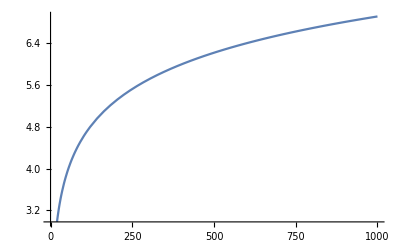

```mathematica
Plot[Log[x],{x,0,1000}]
```

Gráfica e^x de -10 a 10

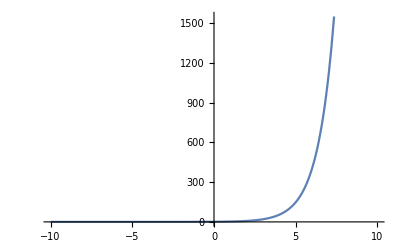

```mathematica
Plot[Exp[x],{x,-10,10}]
```

Gráfica e^-x de -10 a 10

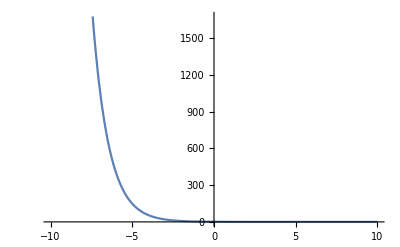

```mathematica
Plot[Exp[-x],{x,-10,10}]
```

Hacer una expansión de potencias de todas las funciones trigonométricas alrededor de cero con 10 términos cada una.

```mathematica
Plot[{Sin[x],Evaluate[Normal[Series[Sin[x],{x,0,21}]]]},{x,-3 Pi, 3 Pi}, PlotLabel->"Expansión de Taylor de Sin[x]", PlotLabels->Automatic]
```

-Graphics-

```mathematica
Plot[{Cos[x],Evaluate[Normal[Series[Cos[x],{x,0,21}]]]},{x,-3 Pi, 3 Pi}, PlotLabel->"Expansión de Taylor de Cos[x]", PlotLabels->Automatic]
```

-Graphics-

```mathematica
Plot[{Tan[x],Evaluate[Normal[Series[Tan[x],{x,0,21}]]]},{x,-2, 2}, PlotLabel->"Expansión de Taylor de Tan[x]", PlotLabels->Automatic]
```

-Graphics-

```mathematica
Plot[{Sec[x],Evaluate[Normal[Series[Sec[x],{x,0,21}]]]},{x,-2, 2}, PlotLabel->"Expansión de Taylor de Sec[x]", PlotLabels->Automatic]
```

-Graphics-

```mathematica
Plot[{Csc[x],Evaluate[Normal[Series[Csc[x],{x,0,21}]]]},{x,0, Pi}, PlotLabel->"Expansión de Taylor de Csc[x]", PlotLabels->Automatic]
```

-Graphics-

```mathematica
Plot[{Cot[x],Evaluate[Normal[Series[Cot[x],{x,0,21}]]]},{x,-Pi, Pi}, PlotLabel->"Expansión de Taylor de Cot[x]", PlotLabels->Automatic]
```

-Graphics-

Repetir el ejercicio

```mathematica
Normal[Series[Sin[x],{x,a,10}]]
```

(-a+x) Cos[a]-1/6 (-a+x)^3 Cos[a]+1/120 (-a+x)^5 Cos[a]-((-a+x)^7 Cos[a])/5040+((-a+x)^9 Cos[a])/362880+Sin[a]-1/2 (-a+x)^2 Sin[a]+1/24 (-a+x)^4 Sin[a]-1/720 (-a+x)^6 Sin[a]+((-a+x)^8 Sin[a])/40320-((-a+x)^10 Sin[a])/3628800

```mathematica
Normal[Series[Cos[x],{x,a,10}]]
```

Cos[a]-1/2 (-a+x)^2 Cos[a]+1/24 (-a+x)^4 Cos[a]-1/720 (-a+x)^6 Cos[a]+((-a+x)^8 Cos[a])/40320-((-a+x)^10 Cos[a])/3628800-(-a+x) Sin[a]+1/6 (-a+x)^3 Sin[a]-1/120 (-a+x)^5 Sin[a]+((-a+x)^7 Sin[a])/5040-((-a+x)^9 Sin[a])/362880

```mathematica
Normal[Series[Tan[x],{x,a,10}]]
```

Tan[a]+(-a+x) (1+Tan[a]^2)+(-a+x)^2 (Tan[a]+Tan[a]^3)+(-a+x)^3 (1/3+Tan[a]^2/2+Tan[a] ((5 Tan[a])/6+Tan[a]^3))+(-a+x)^4 ((17 Tan[a])/24+Tan[a]^3-1/2 Tan[a] (1/2+Tan[a]^2)+Tan[a] (5/24+(7 Tan[a]^2)/6+Tan[a]^4))+(-a+x)^5 (13/60+(29 Tan[a]^2)/24+Tan[a]^4+1/6 (-1/2-Tan[a]^2)-1/2 Tan[a] ((5 Tan[a])/6+Tan[a]^3)+Tan[a] ((61 Tan[a])/120+(3 Tan[a]^3)/2+Tan[a]^5))+(-a+x)^6 ((371 Tan[a])/720+(3 Tan[a]^3)/2+Tan[a]^5+1/24 Tan[a] (1/2+Tan[a]^2)+1/6 (-(5 Tan[a])/6-Tan[a]^3)-1/2 Tan[a] (5/24+(7 Tan[a]^2)/6+Tan[a]^4)+Tan[a] (61/720+(331 Tan[a]^2)/360+(11 Tan[a]^4)/6+Tan[a]^6))+(-a+x)^7 (71/840+(661 Tan[a]^2)/720+(11 Tan[a]^4)/6+Tan[a]^6+1/120 (1/2+Tan[a]^2)+1/24 Tan[a] ((5 Tan[a])/6+Tan[a]^3)+1/6 (-5/24-(7 Tan[a]^2)/6-Tan[a]^4)-1/2 Tan[a] ((61 Tan[a])/120+(3 Tan[a]^3)/2+Tan[a]^5)+Tan[a] ((277 Tan[a])/1008+(173 Tan[a]^3)/120+(13 Tan[a]^5)/6+Tan[a]^7))+(-a+x)^8 ((3691 Tan[a])/13440+(173 Tan[a]^3)/120+(13 Tan[a]^5)/6+Tan[a]^7-1/720 Tan[a] (1/2+Tan[a]^2)+1/120 ((5 Tan[a])/6+Tan[a]^3)+1/24 Tan[a] (5/24+(7 Tan[a]^2)/6+Tan[a]^4)+1/6 (-(61 Tan[a])/120-(3 Tan[a]^3)/2-Tan[a]^5)-1/2 Tan[a] (61/720+(331 Tan[a]^2)/360+(11 Tan[a]^4)/6+Tan[a]^6)+Tan[a] (277/8064+(3071 Tan[a]^2)/5040+(83 Tan[a]^4)/40+(5 Tan[a]^6)/2+Tan[a]^8))+(-a+x)^9 (6233/181440+(24569 Tan[a]^2)/40320+(83 Tan[a]^4)/40+(5 Tan[a]^6)/2+Tan[a]^8+(-1/2-Tan[a]^2)/5040-1/720 Tan[a] ((5 Tan[a])/6+Tan[a]^3)+1/120 (5/24+(7 Tan[a]^2)/6+Tan[a]^4)+1/24 Tan[a] ((61 Tan[a])/120+(3 Tan[a]^3)/2+Tan[a]^5)+1/6 (-61/720-(331 Tan[a]^2)/360-(11 Tan[a]^4)/6-Tan[a]^6)-1/2 Tan[a] ((277 Tan[a])/1008+(173 Tan[a]^3)/120+(13 Tan[a]^5)/6+Tan[a]^7)+Tan[a] ((50521 Tan[a])/362880+(3403 Tan[a]^3)/3024+(203 Tan[a]^5)/72+(17 Tan[a]^7)/6+Tan[a]^9))+(-a+x)^10 ((505219 Tan[a])/3628800+(3403 Tan[a]^3)/3024+(203 Tan[a]^5)/72+(17 Tan[a]^7)/6+Tan[a]^9+(Tan[a] (1/2+Tan[a]^2))/40320+(-(5 Tan[a])/6-Tan[a]^3)/5040-1/720 Tan[a] (5/24+(7 Tan[a]^2)/6+Tan[a]^4)+1/120 ((61 Tan[a])/120+(3 Tan[a]^3)/2+Tan[a]^5)+1/24 Tan[a] (61/720+(331 Tan[a]^2)/360+(11 Tan[a]^4)/6+Tan[a]^6)+1/6 (-(277 Tan[a])/1008-(173 Tan[a]^3)/120-(13 Tan[a]^5)/6-Tan[a]^7)-1/2 Tan[a] (277/8064+(3071 Tan[a]^2)/5040+(83 Tan[a]^4)/40+(5 Tan[a]^6)/2+Tan[a]^8)+Tan[a] (50521/3628800+(94723 Tan[a]^2)/259200+(28121 Tan[a]^4)/15120+(147 Tan[a]^6)/40+(19 Tan[a]^8)/6+Tan[a]^10))

```mathematica
Normal[Series[Cot[x],{x,a,10}]]
```

Cot[a]+(-a+x) (-1-Cot[a]^2)+(-a+x)^2 (Cot[a]+Cot[a]^3)+(-a+x)^3 (-1/3-Cot[a]^2/2+Cot[a] (-(5 Cot[a])/6-Cot[a]^3))+(-a+x)^4 ((17 Cot[a])/24+Cot[a]^3-1/2 Cot[a] (1/2+Cot[a]^2)+Cot[a] (5/24+(7 Cot[a]^2)/6+Cot[a]^4))+(-a+x)^5 (-13/60-(29 Cot[a]^2)/24-Cot[a]^4+1/6 (1/2+Cot[a]^2)-1/2 Cot[a] (-(5 Cot[a])/6-Cot[a]^3)+Cot[a] (-(61 Cot[a])/120-(3 Cot[a]^3)/2-Cot[a]^5))+(-a+x)^6 ((371 Cot[a])/720+(3 Cot[a]^3)/2+Cot[a]^5+1/24 Cot[a] (1/2+Cot[a]^2)+1/6 (-(5 Cot[a])/6-Cot[a]^3)-1/2 Cot[a] (5/24+(7 Cot[a]^2)/6+Cot[a]^4)+Cot[a] (61/720+(331 Cot[a]^2)/360+(11 Cot[a]^4)/6+Cot[a]^6))+(-a+x)^7 (-71/840-(661 Cot[a]^2)/720-(11 Cot[a]^4)/6-Cot[a]^6+1/120 (-1/2-Cot[a]^2)+1/24 Cot[a] (-(5 Cot[a])/6-Cot[a]^3)+1/6 (5/24+(7 Cot[a]^2)/6+Cot[a]^4)-1/2 Cot[a] (-(61 Cot[a])/120-(3 Cot[a]^3)/2-Cot[a]^5)+Cot[a] (-(277 Cot[a])/1008-(173 Cot[a]^3)/120-(13 Cot[a]^5)/6-Cot[a]^7))+(-a+x)^8 ((3691 Cot[a])/13440+(173 Cot[a]^3)/120+(13 Cot[a]^5)/6+Cot[a]^7-1/720 Cot[a] (1/2+Cot[a]^2)+1/120 ((5 Cot[a])/6+Cot[a]^3)+1/24 Cot[a] (5/24+(7 Cot[a]^2)/6+Cot[a]^4)+1/6 (-(61 Cot[a])/120-(3 Cot[a]^3)/2-Cot[a]^5)-1/2 Cot[a] (61/720+(331 Cot[a]^2)/360+(11 Cot[a]^4)/6+Cot[a]^6)+Cot[a] (277/8064+(3071 Cot[a]^2)/5040+(83 Cot[a]^4)/40+(5 Cot[a]^6)/2+Cot[a]^8))+(-a+x)^9 (-6233/181440-(24569 Cot[a]^2)/40320-(83 Cot[a]^4)/40-(5 Cot[a]^6)/2-Cot[a]^8+(1/2+Cot[a]^2)/5040-1/720 Cot[a] (-(5 Cot[a])/6-Cot[a]^3)+1/120 (-5/24-(7 Cot[a]^2)/6-Cot[a]^4)+1/24 Cot[a] (-(61 Cot[a])/120-(3 Cot[a]^3)/2-Cot[a]^5)+1/6 (61/720+(331 Cot[a]^2)/360+(11 Cot[a]^4)/6+Cot[a]^6)-1/2 Cot[a] (-(277 Cot[a])/1008-(173 Cot[a]^3)/120-(13 Cot[a]^5)/6-Cot[a]^7)+Cot[a] (-(50521 Cot[a])/362880-(3403 Cot[a]^3)/3024-(203 Cot[a]^5)/72-(17 Cot[a]^7)/6-Cot[a]^9))+(-a+x)^10 ((505219 Cot[a])/3628800+(3403 Cot[a]^3)/3024+(203 Cot[a]^5)/72+(17 Cot[a]^7)/6+Cot[a]^9+(Cot[a] (1/2+Cot[a]^2))/40320+(-(5 Cot[a])/6-Cot[a]^3)/5040-1/720 Cot[a] (5/24+(7 Cot[a]^2)/6+Cot[a]^4)+1/120 ((61 Cot[a])/120+(3 Cot[a]^3)/2+Cot[a]^5)+1/24 Cot[a] (61/720+(331 Cot[a]^2)/360+(11 Cot[a]^4)/6+Cot[a]^6)+1/6 (-(277 Cot[a])/1008-(173 Cot[a]^3)/120-(13 Cot[a]^5)/6-Cot[a]^7)-1/2 Cot[a] (277/8064+(3071 Cot[a]^2)/5040+(83 Cot[a]^4)/40+(5 Cot[a]^6)/2+Cot[a]^8)+Cot[a] (50521/3628800+(94723 Cot[a]^2)/259200+(28121 Cot[a]^4)/15120+(147 Cot[a]^6)/40+(19 Cot[a]^8)/6+Cot[a]^10))

```mathematica
Normal[Series[Sec[x],{x,a,10}]]
```

Sec[a]+(-a+x) Sec[a] Tan[a]+(-a+x)^2 Sec[a] (1/2+Tan[a]^2)+(-a+x)^3 Sec[a] ((5 Tan[a])/6+Tan[a]^3)+(-a+x)^4 Sec[a] (5/24+(7 Tan[a]^2)/6+Tan[a]^4)+(-a+x)^5 Sec[a] ((61 Tan[a])/120+(3 Tan[a]^3)/2+Tan[a]^5)+(-a+x)^6 Sec[a] (61/720+(331 Tan[a]^2)/360+(11 Tan[a]^4)/6+Tan[a]^6)+(-a+x)^7 Sec[a] ((277 Tan[a])/1008+(173 Tan[a]^3)/120+(13 Tan[a]^5)/6+Tan[a]^7)+(-a+x)^8 Sec[a] (277/8064+(3071 Tan[a]^2)/5040+(83 Tan[a]^4)/40+(5 Tan[a]^6)/2+Tan[a]^8)+(-a+x)^9 Sec[a] ((50521 Tan[a])/362880+(3403 Tan[a]^3)/3024+(203 Tan[a]^5)/72+(17 Tan[a]^7)/6+Tan[a]^9)+(-a+x)^10 Sec[a] (50521/3628800+(94723 Tan[a]^2)/259200+(28121 Tan[a]^4)/15120+(147 Tan[a]^6)/40+(19 Tan[a]^8)/6+Tan[a]^10)

```mathematica
Normal[Series[Csc[x],{x,a,10}]]
```

Csc[a]-(-a+x) Cot[a] Csc[a]+(-a+x)^2 (1/2+Cot[a]^2) Csc[a]+(-a+x)^3 (-(5 Cot[a])/6-Cot[a]^3) Csc[a]+(-a+x)^4 (5/24+(7 Cot[a]^2)/6+Cot[a]^4) Csc[a]+(-a+x)^5 (-(61 Cot[a])/120-(3 Cot[a]^3)/2-Cot[a]^5) Csc[a]+(-a+x)^6 (61/720+(331 Cot[a]^2)/360+(11 Cot[a]^4)/6+Cot[a]^6) Csc[a]+(-a+x)^7 (-(277 Cot[a])/1008-(173 Cot[a]^3)/120-(13 Cot[a]^5)/6-Cot[a]^7) Csc[a]+(-a+x)^8 (277/8064+(3071 Cot[a]^2)/5040+(83 Cot[a]^4)/40+(5 Cot[a]^6)/2+Cot[a]^8) Csc[a]+(-a+x)^9 (-(50521 Cot[a])/362880-(3403 Cot[a]^3)/3024-(203 Cot[a]^5)/72-(17 Cot[a]^7)/6-Cot[a]^9) Csc[a]+(-a+x)^10 (50521/3628800+(94723 Cot[a]^2)/259200+(28121 Cot[a]^4)/15120+(147 Cot[a]^6)/40+(19 Cot[a]^8)/6+Cot[a]^10) Csc[a]

Hacer una tabla con los valores de x y cos(x) de 0 a 10

```mathematica
Table[{x,N[Cos[x]]},{x,0,10}]
```

(0 | 1.
1 | 0.540302
2 | -0.416147
3 | -0.989992
4 | -0.653644
5 | 0.283662
6 | 0.96017
7 | 0.753902
8 | -0.1455
9 | -0.91113
10 | -0.839072)

Hacer una tabla con los valores de x y log(x) de 0 a 100

```mathematica
Table[{x,N[Log[x]]},{x,0,100}]
```

(0 | -∞
1 | 0.
2 | 0.693147
3 | 1.09861
4 | 1.38629
5 | 1.60944
6 | 1.79176
7 | 1.94591
8 | 2.07944
9 | 2.19722
10 | 2.30259
11 | 2.3979
12 | 2.48491
13 | 2.56495
14 | 2.63906
15 | 2.70805
16 | 2.77259
17 | 2.83321
18 | 2.89037
19 | 2.94444
20 | 2.99573
21 | 3.04452
22 | 3.09104
23 | 3.13549
24 | 3.17805
25 | 3.21888
26 | 3.2581
27 | 3.29584
28 | 3.3322
29 | 3.3673
30 | 3.4012
31 | 3.43399
32 | 3.46574
33 | 3.49651
34 | 3.52636
35 | 3.55535
36 | 3.58352
37 | 3.61092
38 | 3.63759
39 | 3.66356
40 | 3.68888
41 | 3.71357
42 | 3.73767
43 | 3.7612
44 | 3.78419
45 | 3.80666
46 | 3.82864
47 | 3.85015
48 | 3.8712
49 | 3.89182
50 | 3.91202
51 | 3.93183
52 | 3.95124
53 | 3.97029
54 | 3.98898
55 | 4.00733
56 | 4.02535
57 | 4.04305
58 | 4.06044
59 | 4.07754
60 | 4.09434
61 | 4.11087
62 | 4.12713
63 | 4.14313
64 | 4.15888
65 | 4.17439
66 | 4.18965
67 | 4.20469
68 | 4.21951
69 | 4.23411
70 | 4.2485
71 | 4.26268
72 | 4.27667
73 | 4.29046
74 | 4.30407
75 | 4.31749
76 | 4.33073
77 | 4.34381
78 | 4.35671
79 | 4.36945
80 | 4.38203
81 | 4.39445
82 | 4.40672
83 | 4.41884
84 | 4.43082
85 | 4.44265
86 | 4.45435
87 | 4.46591
88 | 4.47734
89 | 4.48864
90 | 4.49981
91 | 4.51086
92 | 4.52179
93 | 4.5326
94 | 4.54329
95 | 4.55388
96 | 4.56435
97 | 4.57471
98 | 4.58497
99 | 4.59512
100 | 4.60517)